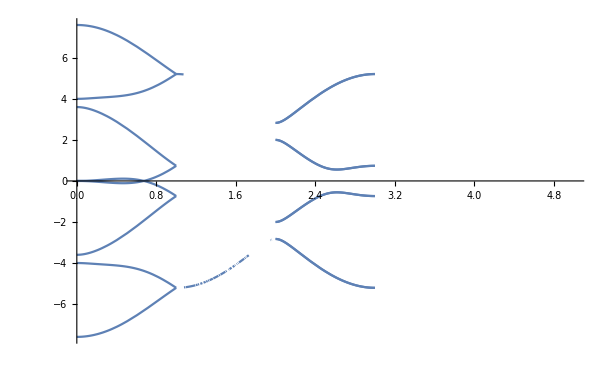

```mathematica
k1f[s_]:=(s-π)HeavisideTheta[π-s]+(s-2π)*HeavisideTheta[2π-s]+(3π-s)*HeavisideTheta[3π-s]+(4π-s)*HeavisideTheta[4π-s]+(s-4π)HeavisideTheta[5π-s];
k2f[s_]:=(π-s)HeavisideTheta[π-s]+(s-2π)HeavisideTheta[2π-s]+(s-3π)HeavisideTheta[3π-s]+(8π-2s)HeavisideTheta[4π-s]+(s-4π)HeavisideTheta[5π-s];
H[t1_,t2_,t3_,t4_,k1_,k2_]:={{0,t1,-ⅈ (1+ⅇ^(-ⅈ k1)) t3,0,0,ⅇ^(ⅈ k2) t1,ⅈ (1+ⅇ^(ⅈ k2)) t3,t2},{t1,0,t2,-ⅈ (1+ⅇ^(ⅈ k2)) t4,ⅇ^(ⅈ k2) t1,0,0,ⅈ (1+ⅇ^(ⅈ k1)) t4},{ⅈ (1+ⅇ^(ⅈ k1)) t3,t2,0,t1,-ⅈ (1+ⅇ^(-ⅈ k2)) t3,0,0,ⅇ^(ⅈ k1) t1},{0,ⅈ (1+ⅇ^(-ⅈ k2)) t4,t1,0,t2,-ⅈ (1+ⅇ^(ⅈ k1)) t4,ⅇ^(ⅈ k1) t1,0},{0,ⅇ^(-ⅈ k2) t1,ⅈ (1+ⅇ^(-ⅈ k2)) t3,t2,0,t1,-ⅈ (1+ⅇ^(ⅈ k1)) t3,0},{ⅇ^(-ⅈ k2) t1,0,0,ⅈ (1+ⅇ^(-ⅈ k1)) t4,t1,0,t2,-ⅈ (1+ⅇ^(-ⅈ k2)) t4},{-ⅈ (1+ⅇ^(-ⅈ k2)) t3,0,0,ⅇ^(-ⅈ k1) t1,ⅈ (1+ⅇ^(-ⅈ k1)) t3,t2,0,t1},{t2,-ⅈ (1+ⅇ^(-ⅈ k1)) t4,ⅇ^(-ⅈ k1) t1,0,0,ⅈ (1+ⅇ^(ⅈ k2)) t4,t1,0}}
With[{t1=1.0,t2=2.0,t3=1.4,t4=1.4},Plot[Sort[Eigenvalues[N[H[t1,t2,t3,t4,k1f[s*π],k2f[s*π]]]]],{s,0,5}]]
```

```mathematica
Eigenvalues[N[H[t1,t2,t3,t4,k1f[s*π],k2f[s*π]]]]
```